# Back-reaction of Fermions

## Fermions in BG of condensate

### Fermion density calculations

```mathematica
Clear[Λ,A1,c1,c2,g]
```

```mathematica
Λ[t_]=JacobiDN[g c1 (t+c2),-1]-I JacobiCN[g c1(t+c2),-1]
```

-ⅈ JacobiCN[c1 g (c2+t),-1]+JacobiDN[c1 g (c2+t),-1]

```mathematica
x[t_]=A1 Λ[t]^(-1/2)
```

A1/(√(-ⅈ JacobiCN[c1 g (c2+t),-1]+JacobiDN[c1 g (c2+t),-1]))

```mathematica
y1[t_]=c3 Λ[t]^(3/2)+c4 Λ[t]^(-1/2)
```

c4/(√(-ⅈ JacobiCN[c1 g (c2+t),-1]+JacobiDN[c1 g (c2+t),-1]))+c3 (-ⅈ JacobiCN[c1 g (c2+t),-1]+JacobiDN[c1 g (c2+t),-1])^(3/2)

```mathematica
y2[t_]=-c3 Λ[t]^(3/2)+c4 Λ[t]^(-1/2)
```

c4/(√(-ⅈ JacobiCN[c1 g (c2+t),-1]+JacobiDN[c1 g (c2+t),-1]))-c3 (-ⅈ JacobiCN[c1 g (c2+t),-1]+JacobiDN[c1 g (c2+t),-1])^(3/2)

```mathematica
A1=1;c1=1;c2=0;g=0.5;c3=1;c4=1;
```

```mathematica
x[t]
```

1/(√(-ⅈ JacobiCN[0.5 t,-1]+JacobiDN[0.5 t,-1]))

```mathematica
y1[t]
```

1/(√(-ⅈ JacobiCN[0.5 t,-1]+JacobiDN[0.5 t,-1]))+(-ⅈ JacobiCN[0.5 t,-1]+JacobiDN[0.5 t,-1])^(3/2)

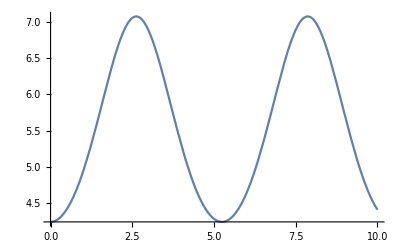

```mathematica
Plot[Re[Conjugate[x[t]]x[t]]+Re[Conjugate[y1[t]]y1[t]],{t,0,10}]
```

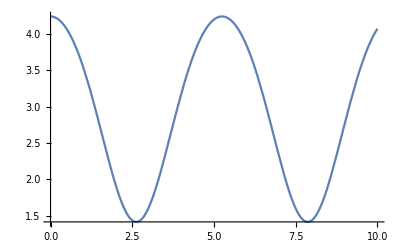

```mathematica
Plot[Re[Conjugate[x[t]]x[t]]+Re[Conjugate[y2[t]]y2[t]],{t,0,10}]
```

```mathematica
Plot[Re[Conjugate[x[t]]x[t]]+Re[Conjugate[y1[t]]y1[t]]+Re[Conjugate[x[t]]x[t]]+Re[Conjugate[y2[t]]y2[t]],{t,0,10}]
```

-Graphics-

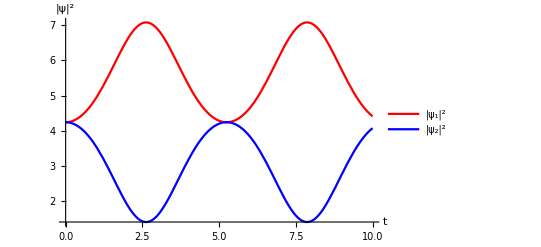

```mathematica
Plot[{Re[Conjugate[x[t]]x[t]]+Re[Conjugate[y1[t]]y1[t]],Re[Conjugate[x[t]]x[t]]+Re[Conjugate[y2[t]]y2[t]]},{t,0,10},AxesLabel->{"t","|ψ|^2"},PlotStyle->{Red,Blue},PlotLegends->{"|ψ_1|^2","|ψ_2|^2"}]
```

### Fermion current density calculations

#### Gamma Matrices (Weyl basis)

```mathematica
g0={{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}}
```

{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}}

```mathematica
g1={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}}
```

{{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}}

```mathematica
g2={{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}}
```

{{0,0,0,-ⅈ},{0,0,ⅈ,0},{0,ⅈ,0,0},{-ⅈ,0,0,0}}

```mathematica
g3={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}}
```

{{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}}

```mathematica
gamma={g0,g1,g2,g3}
```

{{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}},{{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}},{{0,0,0,-ⅈ},{0,0,ⅈ,0},{0,ⅈ,0,0},{-ⅈ,0,0,0}},{{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}}}

#### Current density ((j^ν)^a)

```mathematica
ψ1={0,ψ1l2,0,0};ψ2={ψ2l1,0,0,0};
```

```mathematica
ψ={ψ1,ψ2};
```

```mathematica
TUdd=1/2{{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
```

```mathematica
jUU=Table[Sum[TUdd[[a]][[i]][[j]] (ConjugateTranspose[ψ[[i]]].(gamma[[1]].gamma[[k]]).ψ[[j]]),{i,1,2},{j,1,2}],{k,1,4},{a,1,3}]
```

{{0,0,1/2 ψ1l2 Conjugate[ψ1l2]-1/2 ψ2l1 Conjugate[ψ2l1]},{-1/2 ψ2l1 Conjugate[ψ1l2]-1/2 ψ1l2 Conjugate[ψ2l1],1/2 ⅈ ψ2l1 Conjugate[ψ1l2]-1/2 ⅈ ψ1l2 Conjugate[ψ2l1],0},{-1/2 ⅈ ψ2l1 Conjugate[ψ1l2]+1/2 ⅈ ψ1l2 Conjugate[ψ2l1],-1/2 ψ2l1 Conjugate[ψ1l2]-1/2 ψ1l2 Conjugate[ψ2l1],0},{0,0,1/2 ψ1l2 Conjugate[ψ1l2]+1/2 ψ2l1 Conjugate[ψ2l1]}}

```mathematica
%//MatrixForm
```

(0 | 0 | 1/2 ψ1l2 Conjugate[ψ1l2]-1/2 ψ2l1 Conjugate[ψ2l1]
-1/2 ψ2l1 Conjugate[ψ1l2]-1/2 ψ1l2 Conjugate[ψ2l1] | 1/2 ⅈ ψ2l1 Conjugate[ψ1l2]-1/2 ⅈ ψ1l2 Conjugate[ψ2l1] | 0
-1/2 ⅈ ψ2l1 Conjugate[ψ1l2]+1/2 ⅈ ψ1l2 Conjugate[ψ2l1] | -1/2 ψ2l1 Conjugate[ψ1l2]-1/2 ψ1l2 Conjugate[ψ2l1] | 0
0 | 0 | 1/2 ψ1l2 Conjugate[ψ1l2]+1/2 ψ2l1 Conjugate[ψ2l1])

## Back-reaction equations

```mathematica
Clear[g]
```

For j^03 component,

```mathematica
Λ1[t_]=-ⅈ JacobiCN[g t,-1]+JacobiDN[g  t,-1]
```

-ⅈ JacobiCN[g t,-1]+JacobiDN[g t,-1]

```mathematica
j1=1+Λ1[t]^2//Expand
```

1-JacobiCN[g t,-1]^2-2 ⅈ JacobiCN[g t,-1] JacobiDN[g t,-1]+JacobiDN[g t,-1]^2

```mathematica
j2=1-Λ1[t]^2//Expand
```

1+JacobiCN[g t,-1]^2+2 ⅈ JacobiCN[g t,-1] JacobiDN[g t,-1]-JacobiDN[g t,-1]^2

```mathematica
j11=1-JacobiCN[g t,-1]^2+2 ⅈ JacobiCN[g t,-1] JacobiDN[g t,-1]+JacobiDN[g t,-1]^2
```

1-JacobiCN[g t,-1]^2+2 ⅈ JacobiCN[g t,-1] JacobiDN[g t,-1]+JacobiDN[g t,-1]^2

```mathematica
j22=1+JacobiCN[g t,-1]^2-2 ⅈ JacobiCN[g t,-1] JacobiDN[g t,-1]-JacobiDN[g t,-1]^2
```

1+JacobiCN[g t,-1]^2-2 ⅈ JacobiCN[g t,-1] JacobiDN[g t,-1]-JacobiDN[g t,-1]^2

```mathematica
j1 j11 -j2 j22 //Expand//Simplify
```

-4 JacobiCN[g t,-1]^2+4 JacobiDN[g t,-1]^2

```mathematica
j11 j2 -j22 j1 //Expand//Simplify
```

8 ⅈ JacobiCN[g t,-1] JacobiDN[g t,-1]

```mathematica
(1-JacobiCN[g t,-1]^2-2 ⅈ JacobiCN[g t,-1] JacobiDN[g t,-1]+JacobiDN[g t,-1]^2)(1-JacobiCN[g t,-1]^2+2 ⅈ JacobiCN[g t,-1] JacobiDN[g t,-1]+JacobiDN[g t,-1]^2)//Expand//Simplify
```

JacobiCN[g t,-1]^4+2 JacobiCN[g t,-1]^2 (-1+JacobiDN[g t,-1]^2)+(1+JacobiDN[g t,-1]^2)^2

```mathematica
(1+JacobiCN[g t,-1]^2+2 ⅈ JacobiCN[g t,-1] JacobiDN[g t,-1]-JacobiDN[g t,-1]^2)(1+JacobiCN[g t,-1]^2-2 ⅈ JacobiCN[g t,-1] JacobiDN[g t,-1]-JacobiDN[g t,-1]^2)//Expand//Simplify
```

JacobiCN[g t,-1]^4+(-1+JacobiDN[g t,-1]^2)^2+2 JacobiCN[g t,-1]^2 (1+JacobiDN[g t,-1]^2)

```mathematica
JacobiCN[g t,-1]^4+2 JacobiCN[g t,-1]^2 (-1+JacobiDN[g t,-1]^2)+(1+JacobiDN[g t,-1]^2)^2-JacobiCN[g t,-1]^4-(-1+JacobiDN[g t,-1]^2)^2-2 JacobiCN[g t,-1]^2 (1+JacobiDN[g t,-1]^2)//Expand//Simplify
```

-4 JacobiCN[g t,-1]^2+4 JacobiDN[g t,-1]^2

```mathematica
c1 D[JacobiSN[c1 t,-1],t]
```

c1^2 JacobiCN[c1 t,-1] JacobiDN[c1 t,-1]

```mathematica
JacobiSN[-I t,-1]
```

-JacobiSN[ⅈ t,-1]

```mathematica
Clear[c1,g]
```

```mathematica
U[t_]=c1  JacobiSN[g c1 t,-1]
```

c1 JacobiSN[c1 g t,-1]

```mathematica
Clear[Z]
```

```mathematica
DSolve[Z'[t]- D[U[t],t]/U[t] Z[t]+(2 √2)/(c1 g) JacobiSN[g c1 t,-1]==0,Z,t]
```

{{Z→Function[{t},-(2 √2 t JacobiSN[c1 g t,-1])/(c1 g)+C[1] JacobiSN[c1 g t,-1]]}}

```mathematica
(*For paper*)
U[t_]=c1  JacobiSN[c1 t,-1]
```

c1 JacobiSN[c1 t,-1]

```mathematica
DSolve[Z'[t]- D[U[t],t]/U[t] Z[t]+(2 √2)/c1 g JacobiSN[ c1 t,-1]==0,Z,t]
```

{{Z→Function[{t},-(2 √2 g t JacobiSN[c1 t,-1])/c1+C[1] JacobiSN[c1 t,-1]]}}

For general equations

```mathematica
Clear[t,x,y,z]
```

```mathematica
coord={t,x,y,z};
n=4;(*# of spacetime dimensions*)
```

```mathematica
(*Minkowski*)
```

```mathematica
gdd={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
gUU= {{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
(*Christoffel  symbols*)
```

```mathematica
ΓUdd=Table[1/2 Sum[gUU[[i]][[l]](D[gdd[[l]][[k]],coord[[j]]]+D[gdd[[l]][[j]],coord[[k]]]-D[ gdd[[j]][[k]],coord[[l]]]),{l,1,n}],{i,1,n},{j,1,n},{k,1,n}];
```

```mathematica
(*Gauge field A with 'a' as internal index and d as spacetime index= Aad*)
```

```mathematica
m=3;(*# of internal indices (SU(2))*)
```

```mathematica
Clear[U]
```

```mathematica
Aad={{0,U[t]+A11[t],A12[t],0},{0,A21[t],U[t]+A22[t],0},{0,0,0,U[t]+A33[t]}}
```

{{0,A11[t]+U[t],A12[t],0},{0,A21[t],A22[t]+U[t],0},{0,0,0,A33[t]+U[t]}}

```mathematica
MatrixForm[Aad]
```

(0 | A11[t]+U[t] | A12[t] | 0
0 | A21[t] | A22[t]+U[t] | 0
0 | 0 | 0 | A33[t]+U[t])

```mathematica
Clear[g]
```

```mathematica
Fadd=Table[D[Aad[[a]][[j]],coord[[i]]]- D[Aad[[a]][[i]],coord[[j]]] +Sum[LeviCivitaTensor[3] [[a,b,c]] Aad[[b]][[i]]Aad[[c]][[j]],{b,1,m},{c,1,m}],{a,1,m},{i,1,n},{j,1,n}];
```

```mathematica
FaUU=Table[Sum[gUU[[i]][[k]]gUU[[j]][[l]]Fadd[[a]][[k]][[l]],{k,1,n},{l,1,n}],{a,1,m},{i,1,n},{j,1,n}];
```

```mathematica
Sum[FaUU[[a]][[i]][[j]]Fadd[[a]][[i]][[j]],{a,1,m},{i,1,n},{j,1,n}]
```

2 A12[t]^2 (A33[t]+U[t])^2+2 A21[t]^2 (A33[t]+U[t])^2+2 (A11[t]+U[t])^2 (A33[t]+U[t])^2+2 (A22[t]+U[t])^2 (A33[t]+U[t])^2+(A12[t] A21[t]-(A11[t]+U[t]) (A22[t]+U[t]))^2+(-A12[t] A21[t]+(A11[t]+U[t]) (A22[t]+U[t]))^2+2 A12'[t]^2+2 A21'[t]^2+(-A11'[t]-U'[t])^2+(-A22'[t]-U'[t])^2+(-A33'[t]-U'[t])^2+(A11'[t]+U'[t])^2+(A22'[t]+U'[t])^2+(A33'[t]+U'[t])^2

```mathematica
%//Expand
```

2 A12[t]^2 A21[t]^2-4 A11[t] A12[t] A21[t] A22[t]+2 A11[t]^2 A22[t]^2+2 A11[t]^2 A33[t]^2+2 A12[t]^2 A33[t]^2+2 A21[t]^2 A33[t]^2+2 A22[t]^2 A33[t]^2-4 A11[t] A12[t] A21[t] U[t]+4 A11[t]^2 A22[t] U[t]-4 A12[t] A21[t] A22[t] U[t]+4 A11[t] A22[t]^2 U[t]+4 A11[t]^2 A33[t] U[t]+4 A12[t]^2 A33[t] U[t]+4 A21[t]^2 A33[t] U[t]+4 A22[t]^2 A33[t] U[t]+4 A11[t] A33[t]^2 U[t]+4 A22[t] A33[t]^2 U[t]+4 A11[t]^2 U[t]^2+2 A12[t]^2 U[t]^2-4 A12[t] A21[t] U[t]^2+2 A21[t]^2 U[t]^2+8 A11[t] A22[t] U[t]^2+4 A22[t]^2 U[t]^2+8 A11[t] A33[t] U[t]^2+8 A22[t] A33[t] U[t]^2+4 A33[t]^2 U[t]^2+8 A11[t] U[t]^3+8 A22[t] U[t]^3+8 A33[t] U[t]^3+6 U[t]^4+2 A11'[t]^2+2 A12'[t]^2+2 A21'[t]^2+2 A22'[t]^2+2 A33'[t]^2+4 A11'[t] U'[t]+4 A22'[t] U'[t]+4 A33'[t] U'[t]+6 U'[t]^2

```mathematica
(*∇_μ F^μν*)
CovDFaUU=Table[Sum[D[FaUU[[a]][[k]][[j]],coord[[k]]] +
Sum[ ΓUdd[[k]][[k]][[l]] FaUU[[a]][[l]][[j]] + ΓUdd[[j]][[k]][[l]]FaUU[[a]][[k]][[l]],{l,1,n}] ,{k,1,n}],{a,1,m},{j,1,n}];
(*g Subscript[f, abc] Subscript[A, μ]^b F^cμν*)
NonaU=Table[Sum[LeviCivitaTensor[3] [[a,b,c]] Aad[[b]][[i]] FaUU[[c]][[i]][[j]],{b,1,m},{c,1,m},{i,1,n}],{a,1,m},{j,1,n}];
(*∇_μ F^μν+g Subscript[f, abc] Subscript[A, μ]^b F^cμν*)
YMeq=CovDFaUU+NonaU;
```

```mathematica
YMeq[[1]]//MatrixForm
```

(0
-((A11[t]+U[t]) (A33[t]+U[t])^2)+(A22[t]+U[t]) (A12[t] A21[t]-(A11[t]+U[t]) (A22[t]+U[t]))+A11''[t]+U''[t]
-A12[t] (A33[t]+U[t])^2+A21[t] (-A12[t] A21[t]+(A11[t]+U[t]) (A22[t]+U[t]))+A12''[t]
0)

```mathematica
Table[Conjugate[JacobiCN[-a I ,-1]],{a,0,20,0.5}]//N
```

{1.+0. ⅈ,1.11665+0. ⅈ,1.35051+0. ⅈ,1.38963+0. ⅈ,1.17286+0. ⅈ,1.00742+0. ⅈ,1.06877+0. ⅈ,1.29845+0. ⅈ,1.41106+0. ⅈ,1.23333+0. ⅈ,1.02934+0. ⅈ,1.03219+0. ⅈ,1.2392+0. ⅈ,1.41207+0. ⅈ,1.29296+0. ⅈ,1.06471+0. ⅈ,1.00891+0. ⅈ,1.17858+0. ⅈ,1.39252+0. ⅈ,1.34597+0. ⅈ,1.11161+0. ⅈ,1.00007+0. ⅈ,1.12176+0. ⅈ,1.35494+0. ⅈ,1.38656+0. ⅈ,1.16718+0. ⅈ,1.00606+0. ⅈ,1.07293+0. ⅈ,1.30388+0. ⅈ,1.40986+0. ⅈ,1.22744+0. ⅈ,1.02662+0. ⅈ,1.03516+0. ⅈ,1.24507+0. ⅈ,1.41289+0. ⅈ,1.2874+0. ⅈ,1.06076+0. ⅈ,1.01054+0. ⅈ,1.18433+0. ⅈ,1.39525+0. ⅈ,1.34131+0. ⅈ}

```mathematica
Conjugate[JacobiCN[I t,-1]]
```

Conjugate[JacobiCN[ⅈ t,-1]]

Solving

```mathematica
JacobiDN[-I t,-1]
```

JacobiDN[ⅈ t,-1]

```mathematica
DSolve[s''[t]-k g^2 JacobiSN[g t,-1]^3==0,s,t]
```

{{s→Function[{t},C[1]+t C[2]-1/2 k JacobiSN[g t,-1]]}}

```mathematica
DSolve[s''[t]-g^2 c1^2((-2 √2)/(g c1)  t+k)JacobiSN[g c1  t,-1]^3-2 √2  JacobiCN[g c1 t,-1]JacobiDN[g c1  t,-1]==0,s,t]
```

{{s→Function[{t},-(√2 ArcTan[JacobiCD[c1 g t,-1]])/(c1^2 g^2)+C[1]+t C[2]-(-2 √2 ArcTan[JacobiCD[c1 g t,-1]]+c1 g (c1 g k-2 √2 t) JacobiSN[c1 g t,-1])/(2 c1^2 g^2)]}}

```mathematica
-(√2 ArcTan[JacobiCD[c1 g t,-1]])/(c1^2 g^2)+C[1]+t C[2]-(-2 √2 ArcTan[JacobiCD[c1 g t,-1]]+c1 g (c1 g k-2 √2 t) JacobiSN[c1 g t,-1])/(2 c1^2 g^2)//Simplify
```

C[1]+t C[2]+(-k/2+(√2 t)/(c1 g)) JacobiSN[c1 g t,-1]

```mathematica
(*For paper*)
```

```mathematica
DSolve[s''[t]-c1^2((-2 √2)/c1 g  t+k)JacobiSN[ c1  t,-1]^3-2 √2 g JacobiCN[ c1 t,-1]JacobiDN[ c1  t,-1]==0,s,t]
```

{{s→Function[{t},-(√2 g ArcTan[JacobiCD[c1 t,-1]])/c1^2+C[1]+t C[2]-(-2 √2 g ArcTan[JacobiCD[c1 t,-1]]+c1 (c1 k-2 √2 g t) JacobiSN[c1 t,-1])/(2 c1^2)]}}

```mathematica
-(√2 g ArcTan[JacobiCD[c1 t,-1]])/c1^2+C[1]+t C[2]-(-2 √2 g ArcTan[JacobiCD[c1 t,-1]]+c1 (c1 k-2 √2 g t) JacobiSN[c1 t,-1])/(2 c1^2)//Simplify
```

C[1]+t C[2]+(-k/2+(√2 g t)/c1) JacobiSN[c1 t,-1]

```mathematica
Clear[t]
```

```mathematica
DSolve[s''[t]+6 JacobiSN[ t,-1]^2 s[t]==0,s,t]
```

DSolve[6 JacobiSN[t,-1]^2 s[t]+s''[t]==0,s,t]

```mathematica
Clear[x]
```

```mathematica
DSolve[(1+Sin[x]^2)y''[x]+1/2 Sin[2x]y'[x]+(6 (1)  Sin[x]^2)y[x]==k,y,x]
```

{{y→Function[{x},(C[1] Cos[x] (1-Cos[x]^2)^(1/4) (2-Cos[x]^2)^(3/4))/((2-3 Cos[x]^2+Cos[x]^4)^(1/4))+(C[2] (1-Cos[x]^2)^(1/4) (2-Cos[x]^2)^(3/4) (-2 √((-1+Cos[x]^2)/(-2+Cos[x]^2))+√2 Cos[x] EllipticF[ArcSin[Cos[x]],1/2]))/(4 (2-3 Cos[x]^2+Cos[x]^4)^(1/4))+1/(4 (-2+Cos[x]^2))(-2 k √(1-Cos[x]^2) (2-Cos[x]^2)^(3/2) √((-1+Cos[x]^2)/(-2+Cos[x]^2))+√2 k Cos[x] √(1-Cos[x]^2) (2-Cos[x]^2)^(3/2) EllipticF[ArcSin[Cos[x]],1/2]-2 √2 k Cos[x] (1-Cos[x]^2)^(1/4) (2-Cos[x]^2)^(3/4) ((-1+Cos[x]^2)/(-2+Cos[x]^2))^(1/4) EllipticF[ArcSin[Cos[x]],1/2]+√2 k Cos[x]^3 (1-Cos[x]^2)^(1/4) (2-Cos[x]^2)^(3/4) ((-1+Cos[x]^2)/(-2+Cos[x]^2))^(1/4) EllipticF[ArcSin[Cos[x]],1/2])]}}

```mathematica
1/(4 (-2+Cos[x]^2))(-2 k √(1-Cos[x]^2) (2-Cos[x]^2)^(3/2) √((-1+Cos[x]^2)/(-2+Cos[x]^2))+√2 k Cos[x] √(1-Cos[x]^2) (2-Cos[x]^2)^(3/2) EllipticF[ArcSin[Cos[x]],1/2]-2 √2 k Cos[x] (1-Cos[x]^2)^(1/4) (2-Cos[x]^2)^(3/4) ((-1+Cos[x]^2)/(-2+Cos[x]^2))^(1/4) EllipticF[ArcSin[Cos[x]],1/2]+√2 k Cos[x]^3 (1-Cos[x]^2)^(1/4) (2-Cos[x]^2)^(3/4) ((-1+Cos[x]^2)/(-2+Cos[x]^2))^(1/4) EllipticF[ArcSin[Cos[x]],1/2])//FullSimplify
```

1/2 k Sin[x]^2

```mathematica
y1[x_]=(C[1] Cos[x] (1-Cos[x]^2)^(1/4) (2-Cos[x]^2)^(3/4))/((2-3 Cos[x]^2+Cos[x]^4)^(1/4))+(C[2] (1-Cos[x]^2)^(1/4) (2-Cos[x]^2)^(3/4) (-2 √((-1+Cos[x]^2)/(-2+Cos[x]^2))+√2 Cos[x] EllipticF[ArcSin[Cos[x]],1/2]))/(4 (2-3 Cos[x]^2+Cos[x]^4)^(1/4))+1/2 k Sin[x]^2;
```

```mathematica
DSolve[(1+Sin[x]^2)y''[x]+1/2 Sin[2x]y'[x]+2 Sin[x]^2 y1[x]==k1,y,x]
```

{{y→Function[{x},C[4]+(C[3]/(√(-3+Cos[2 K[1]]))+1/(4 √(-3+Cos[2 K[1]]))((2^(3/4) C[2] (1-Cos[2 K[1]])^(3/4) (3-Cos[2 K[1]])^(1/4) √(-3+Cos[2 K[1]]) Cot[K[1]])/(3 (7-8 Cos[2 K[1]]+Cos[4 K[1]])^(1/4))-(2^(3/4) C[2] (1-Cos[2 K[1]])^(1/4) (3-Cos[2 K[1]])^(3/4) √(-3+Cos[2 K[1]]) √((-1+Cos[2 K[1]])/(-3+Cos[2 K[1]])) Cot[K[1]])/(7-8 Cos[2 K[1]]+Cos[4 K[1]])^(1/4)+4/3 k Cos[K[1]] √(-3+Cos[2 K[1]]) Sin[K[1]]+((-4/3 2^(3/4) C[1]-(8 2^(3/4) C[1])/(3 (-3+Cos[2 K[1]]))) (1-Cos[2 K[1]])^(1/4) (3-Cos[2 K[1]])^(3/4) √(-3+Cos[2 K[1]]) Sin[K[1]])/(7-8 Cos[2 K[1]]+Cos[4 K[1]])^(1/4)+(4 2^(1/4) C[2] (1-Cos[2 K[1]])^(1/4) (3-Cos[2 K[1]])^(3/4) EllipticF[ArcSin[Cos[K[1]]],1/2] Sin[K[1]]^3)/(3 √(-3+Cos[2 K[1]]) (7-8 Cos[2 K[1]]+Cos[4 K[1]])^(1/4))+(8 (k-3 k1) Cos[K[1]] HypergeometricPFQ[{1/4,1/2},{5/4},Sin[K[1]]^4] Sin[K[1]] √(1+Sin[K[1]]^2) (Sin[K[1]]^2+Sin[K[1]]^4)^(1/4))/(3 √(-3+Cos[2 K[1]]) √(1-Sin[K[1]]^2) (Sin[K[1]]^2 (1+Sin[K[1]]^2))^(1/4))))K[1]1x]}}

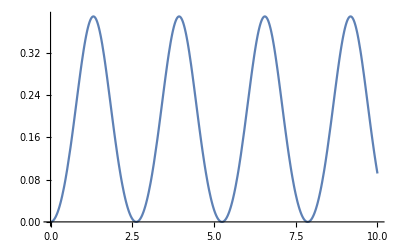

```mathematica
Plot[11/(2 √2)(0.1)  JacobiSN[x,-1]^2,{x,0,10}]
```

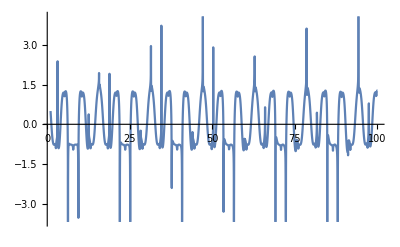

```mathematica
Plot[y1[t],{t,1,100}]
```

```mathematica
(*c1=1,g=0.1*)
```

```mathematica
sol=NDSolve[{y''[t]+6 JacobiSN[t,-1]^2 y[t]-11/(√2)(0.1)==0,z''[t]-3/(√2)(0.1)+2 JacobiSN[t,-1]^2 y[t]==0,w''[t]-5/(√2)(0.1)+2 JacobiSN[t,-1]^2 y[t]==0,w[0]==0,w'[0]==0,y[0]==0,y'[0]==1,z[0]==0,z'[0]==0},{y,z,w},{t,0,100}]
```

{{y→InterpolatingFunction[…],z→InterpolatingFunction[…],w→InterpolatingFunction[…]}}

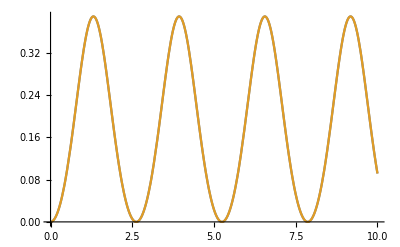

```mathematica
Plot[{Evaluate[-y[t]/.sol],11/(2 √2)(0.1)  JacobiSN[t,-1]^2},{t,0,10},PlotStyle->Automatic]
```

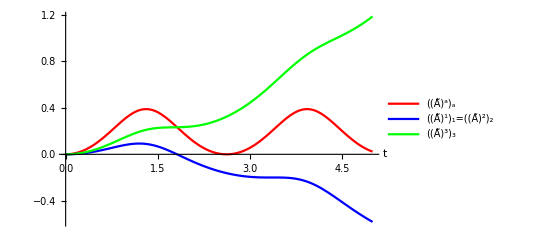

```mathematica
Plot[Evaluate[{y[t],z[t],w[t]}/.sol],{t,0,5},PlotStyle->{Red, Blue,Green},PlotLegends->{"((Ã)^a)_a","((Ã)^1)_1=((Ã)^2)_2","((Ã)^3)_3"},AxesLabel->Automatic]
```

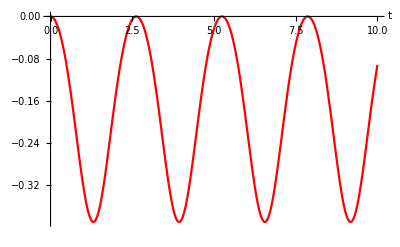

```mathematica
Plot[Evaluate[y[t]/.sol],{t,0,10},PlotStyle->Red,AxesLabel->Automatic]
```

```mathematica
OverTilde[A]
```

Ã

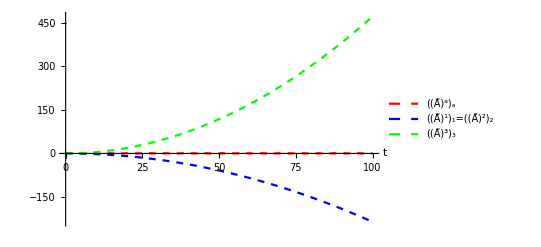

```mathematica
p1=Plot[Evaluate[{y[t],z[t],w[t]}/.sol],{t,0,100},PlotStyle->{{Dashed,Red}, {Dashed,Blue},{Dashed,Green}},PlotLegends->{"((Ã)^a)_a","((Ã)^1)_1=((Ã)^2)_2","((Ã)^3)_3"},AxesLabel->Automatic]
```

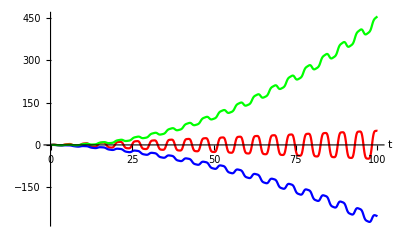

```mathematica
p2=Plot[Evaluate[{y[t],z[t],w[t]}/.sol],{t,0,100},PlotStyle->{Red,Blue,Green},AxesLabel->Automatic]
```

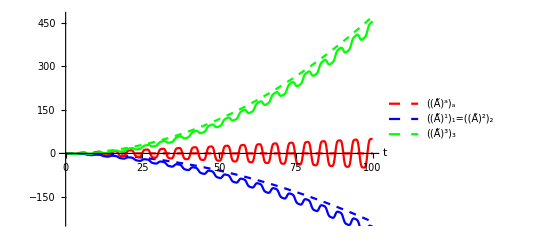

```mathematica
Show[p1,p2]
```

```mathematica
(*For thesis*)
```

```mathematica
(*c1=1,g=0.1*)
```

```mathematica
sol=NDSolve[{y''[t]+6 (0.1)^2 JacobiSN[0.1t,-1]^2 y[t]-11/(√2)==0,z''[t]+2 (0.1)^2 JacobiSN[0.1t,-1]^2 y[t]-3/(√2)==0,w''[t]+2  (0.1)^2 JacobiSN[0.1t,-1]^2 y[t]-5/(√2)==0,y[0]==0,y'[0]==0,w[0]==0,w'[0]==1,z[0]==0,z'[0]==0},{y,z,w},{t,0,100}]
```

{{y→InterpolatingFunction[…],z→InterpolatingFunction[…],w→InterpolatingFunction[…]}}

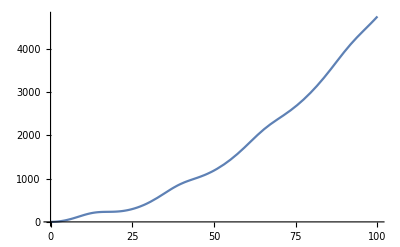

```mathematica
Plot[Evaluate[w[t]/.sol],{t,0,100}]
```

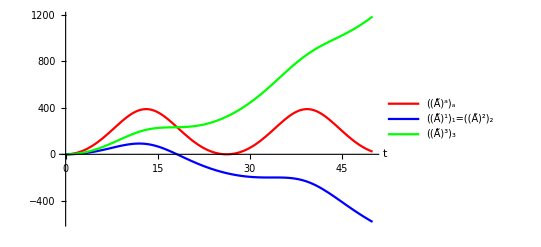

```mathematica
Plot[Evaluate[{y[t],z[t],w[t]}/.sol],{t,0,50},PlotStyle->{Red,Blue,Green},PlotLegends->{"((Ã)^a)_a","((Ã)^1)_1=((Ã)^2)_2","((Ã)^3)_3"},AxesLabel->Automatic]
```

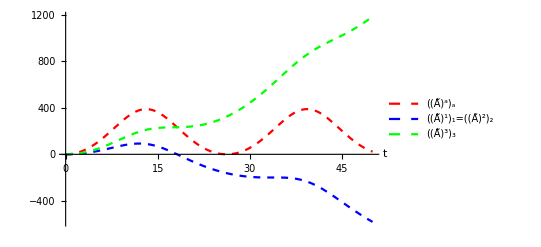

```mathematica
p1=Plot[Evaluate[{y[t],z[t],w[t]}/.sol],{t,0,50},PlotStyle->{{Dashed,Red}, {Dashed,Blue},{Dashed,Green}},PlotLegends->{"((Ã)^a)_a","((Ã)^1)_1=((Ã)^2)_2","((Ã)^3)_3"},AxesLabel->Automatic]
```

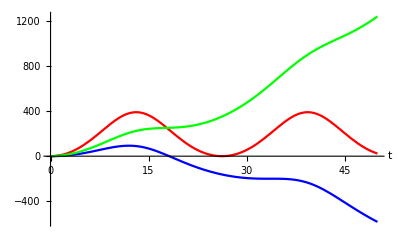

```mathematica
p2=Plot[Evaluate[{y[t],z[t],w[t]}/.sol],{t,0,50},PlotStyle->{Red,Blue,Green},AxesLabel->Automatic]
```

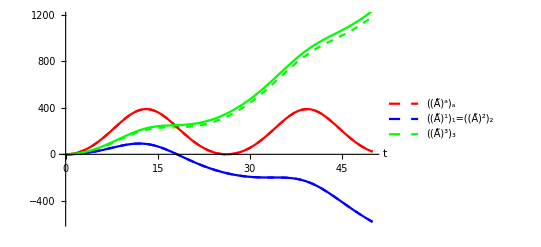

```mathematica
Show[p1,p2]
```